```mathematica
(*---1) Physical/Model Constants---*)k=10; (*K1=k,ignoring higher-order terms (K2)*)
xi=9;
muB=0.057883818060;
mu=4075.90672005*muB;
ga=176.085963023;
al=0.1;
tau0=mu/(2*ga*k);

(*---2) Define the Cubic Anisotropy Energy (Ignoring K2)---*)
Ecubic[θ_,φ_]:=Module[{sx,sy,sz},sx=Sin[θ] Cos[φ];
sy=Sin[θ] Sin[φ];
sz=Cos[θ];
k (sx^2 sy^2+sy^2 sz^2+sz^2 sx^2)];

(*---3) Define the Torque Field:EqTorqueCubic (already known)---*)
dEdTheta=FullSimplify[D[Ecubic[θ,φ],θ]];
dEdPhi=FullSimplify[D[Ecubic[θ,φ],φ]];

EqTorqueCubic[θ_,φ_]:=-{(Csc[θ] dEdPhi+al dEdTheta)/(tau0 (1+al^2)),(al Csc[θ] dEdPhi-dEdTheta)/(tau0 (1+al^2))};

(*---4) Create the VectorPlot for the Cubic Torque---*)cubicPlot=VectorPlot[EqTorqueCubic[θ,φ],{θ,0,Pi},{φ,0,2 Pi},VectorColorFunction->Blue,VectorStyle->{Blue, Arrowheads[0.015]},VectorColorFunctionScaling->False,VectorScaling->Large,VectorPoints->50,VectorAspectRatio->0.1,PlotRange->All,Axes->True,FrameLabel->{"θ (rad)","φ (rad)"}];

(*---5) Create a Simple Grayscale Contour Plot for the Energy---*)
energyContour=ContourPlot[Ecubic[θ,φ],{θ,0,Pi},{φ,0,2 Pi},ColorFunction->(GrayLevel[1-0.5 #]&),ColorFunctionScaling->True,Contours->20,ContourShading->True,PlotRange->All,Frame->True,FrameLabel->{"θ (rad)","φ (rad)"}];

(*---6) Import/Convert Your Paths to (θ,φ)---*)
filePath1="C:\\Users\\abhin\\Desktop\\FePt\\I-II\\3.0d0\\Path_P.out";
filePath2="C:\\Users\\abhin\\Desktop\\FePt\\I-III\\3.0d0\\Path_P.out";
filePath3="C:\\Users\\abhin\\Desktop\\FePt\\II-III\\3.0d0\\Path_P.out";
filePath4="C:\\Users\\abhin\\Desktop\\FePt\\MEP_I-II\\PathG.out";
filePath5="C:\\Users\\abhin\\Desktop\\FePt\\MEP_II-III\\PathG.out";

data1=Import[filePath1,"Table"][[3;;]];
data2=Import[filePath2,"Table"][[3;;]];
data3=Import[filePath3,"Table"][[3;;]];
data4=Import[filePath4,"Table"][[3;;]];
data5=Import[filePath5,"Table"][[3;;]];

sph1=ToSphericalCoordinates/@data1[[All,4;;6]];
sph2=ToSphericalCoordinates/@data2[[All,4;;6]];
sph3=ToSphericalCoordinates/@data3[[All,4;;6]];
sph4=ToSphericalCoordinates/@data4[[All,4;;6]];
sph5=ToSphericalCoordinates/@data5[[All,4;;6]];

θ1=sph1[[All,2]];
φ1=Mod[sph1[[All,3]],2 Pi];
θ2=sph2[[All,2]];
φ2=Mod[sph2[[All,3]],2 Pi];
θ3=sph3[[All,2]];
φ3=Mod[sph3[[All,3]],2 Pi];
θ4=sph4[[All,2]];
φ4=Mod[sph4[[All,3]],2 Pi];
θ5=sph5[[All,2]];
φ5=Mod[sph5[[All,3]],2 Pi];

fractionList={1/6,1/3,1/2,2/3,5/6};

indices1=Round[Length[θ1]*fractionList];
indices2=Round[Length[θ2]*fractionList];
indices3=Round[Length[θ3]*fractionList];

(*Adjust indices to ensure they do not exceed velcartz lengths*)
indices1=Map[Min[#,Length[velcartz1]]&,indices1];
indices2=Map[Min[#,Length[velcartz2]]&,indices2];
indices3=Map[Min[#,Length[velcartz3]]&,indices3];

(*Diagnostic Prints to Verify Lengths*)
Print["Length of θ1: ",Length[θ1]];
Print["Length of velcartz1: ",Length[velcartz1]];
Print["Length of θ2: ",Length[θ2]];
Print["Length of velcartz2: ",Length[velcartz2]];
Print["Length of θ3: ",Length[θ3]];
Print["Length of velcartz3: ",Length[velcartz3]];

Print["Adjusted indices1: ",indices1];
Print["Adjusted indices2: ",indices2];
Print["Adjusted indices3: ",indices3];

(*---9) Create Path Graphics---*)
pathGraphics=Graphics[{(*First path:solid red line*){RGBColor[0.9,0.31,0.67],AbsoluteThickness[5],Line[Transpose[{θ1,φ1}]]},(*Second path:dashed red line with moderate dash pattern*){RGBColor[0.9,0.31,0.67],Dashed,AbsoluteThickness[5],Line[Transpose[{θ4,φ4}]]},(*Third path:green solid line*){Green,AbsoluteThickness[5],Line[Transpose[{θ3,φ3}]]},(*Fourth path:dashed green line*){Directive[Green,Dashed,AbsoluteThickness[5]],Line[Transpose[{θ5,φ5}]]},(*Fifth path:solid orange line*){Orange,AbsoluteThickness[5],Line[Transpose[{θ2,φ2}]]},{Directive[Orange,AbsoluteDashing[1],AbsoluteThickness[5]],Line[Transpose[{Join[θ4,θ5],Join[φ4,φ5]}]]}(*---Added:Dashed Orange Line Combining Existing Dashed Lines with Sparser Dashing---*)}];

(*---8) Create Velocity Arrows Without Tails---*)(*Velocity Arrows for OCP #1 (I-II)*)
velArrows1=Table[{Arrowheads[velmagnitude1[i]/velmagnScaling1],(*Scale arrowhead size*)Arrow[{{θ1[[i]]+velsphercaltheta1[θ1[[i]],φ1[[i]],i]*velvectorScaling1*0.8,φ1[[i]]+velsphercalphi1[θ1[[i]],φ1[[i]],i]*velvectorScaling1*0.8},{θ1[[i]]+velsphercaltheta1[θ1[[i]],φ1[[i]],i]*velvectorScaling1,φ1[[i]]+velsphercalphi1[θ1[[i]],φ1[[i]],i]*velvectorScaling1}}]},{i,indices1}];

(*Velocity Arrows for OCP #2 (I-III)*)
velArrows2=Table[{Arrowheads[velmagnitude2[i]/velmagnScaling2],(*Scale arrowhead size*)Arrow[{{θ2[[i]]+velsphercaltheta2[θ2[[i]],φ2[[i]],i]*velvectorScaling2*0.8,φ2[[i]]+velsphercalphi2[θ2[[i]],φ2[[i]],i]*velvectorScaling2*0.8},{θ2[[i]]+velsphercaltheta2[θ2[[i]],φ2[[i]],i]*velvectorScaling2,φ2[[i]]+velsphercalphi2[θ2[[i]],φ2[[i]],i]*velvectorScaling2}}]},{i,indices2}];

(*Velocity Arrows for OCP #3 (II-III)*)
velArrows3=Table[{Arrowheads[velmagnitude3[i]/velmagnScaling3],(*Scale arrowhead size*)Arrow[{{θ3[[i]]+velsphercaltheta3[θ3[[i]],φ3[[i]],i]*velvectorScaling3*0.8,φ3[[i]]+velsphercalphi3[θ3[[i]],φ3[[i]],i]*velvectorScaling3*0.8},{θ3[[i]]+velsphercaltheta3[θ3[[i]],φ3[[i]],i]*velvectorScaling3,φ3[[i]]+velsphercalphi3[θ3[[i]],φ3[[i]],i]*velvectorScaling3}}]},{i,indices3}];

(*----7) Velocity Import and Calculations (Modified)----*)

(*----Calculation for OCP #1 (I-II)-----*)
velvectorScaling1=0.1; (*Increased scaling for larger arrows*)
velmagnScaling1=20;    (*Decreased scaling for more apparent arrowhead sizing*)
velcartz1=Drop[Import["C:\\Users\\abhin\\Desktop\\FePt\\I-II\\3.0d0\\velocity.out","Table"],2]; (*Import velocity data for OCP #1 and drop the first two lines*)

(*Define velocity magnitude for OCP #1*)
velmagnitude1[i_]:=Sqrt[velcartz1[[i,4]]^2+velcartz1[[i,5]]^2+velcartz1[[i,6]]^2];

(*Define spherical components for OCP #1*)
velsphercaltheta1[θ_,φ_,i_]:=Cos[θ] Cos[φ] velcartz1[[i,4]]+Cos[θ] Sin[φ] velcartz1[[i,5]]-Sin[θ] velcartz1[[i,6]];
velsphercalphi1[θ_,φ_,i_]:=-Sin[φ] velcartz1[[i,4]]+Cos[φ] velcartz1[[i,5]];

(*----Calculation for OCP #2 (I-III)-----*)
velvectorScaling2=0.1; (*Increased scaling for larger arrows*)
velmagnScaling2=20;    (*Decreased scaling for more apparent arrowhead sizing*)
velcartz2=Drop[Import["C:\\Users\\abhin\\Desktop\\FePt\\I-III\\3.0d0\\velocity.out","Table"],2]; (*Import velocity data for OCP #2 and drop the first two lines*)

(*Define velocity magnitude for OCP #2*)
velmagnitude2[i_]:=Sqrt[velcartz2[[i,4]]^2+velcartz2[[i,5]]^2+velcartz2[[i,6]]^2];

(*Define spherical components for OCP #2*)
velsphercaltheta2[θ_,φ_,i_]:=Cos[θ] Cos[φ] velcartz2[[i,4]]+Cos[θ] Sin[φ] velcartz2[[i,5]]-Sin[θ] velcartz2[[i,6]];
velsphercalphi2[θ_,φ_,i_]:=-Sin[φ] velcartz2[[i,4]]+Cos[φ] velcartz2[[i,5]];

(*----Calculation for OCP #3 (II-III)-----*)
velvectorScaling3=0.1; (*Increased scaling for larger arrows*)
velmagnScaling3=20;    (*Decreased scaling for more apparent arrowhead sizing*)
velcartz3=Drop[Import["C:\\Users\\abhin\\Desktop\\FePt\\II-III\\3.0d0\\velocity.out","Table"],2]; (*Import velocity data for OCP #3 and drop the first two lines*)

(*Define velocity magnitude for OCP #3*)
velmagnitude3[i_]:=Sqrt[velcartz3[[i,4]]^2+velcartz3[[i,5]]^2+velcartz3[[i,6]]^2];

(*Define spherical components for OCP #3*)
velsphercaltheta3[θ_,φ_,i_]:=Cos[θ] Cos[φ] velcartz3[[i,4]]+Cos[θ] Sin[φ] velcartz3[[i,5]]-Sin[θ] velcartz3[[i,6]];
velsphercalphi3[θ_,φ_,i_]:=-Sin[φ] velcartz3[[i,4]]+Cos[φ] velcartz3[[i,5]];

(*---10) Create Velocity Graphics---*)
velGraphics1=Graphics[{Purple,velArrows1}];
velGraphics2=Graphics[{Red,velArrows2}];
velGraphics3=Graphics[{Darker[Green,0.4],velArrows3}];

(*---11) Combine All Graphics and Export---*)
combinedPlot=Show[energyContour,(*Background energy contour*)cubicPlot,(*Torque vector field*)pathGraphics,(*Overlayed paths*)velGraphics1,(*Velocity vectors for OCP #1*)velGraphics2,(*Velocity vectors for OCP #2*)velGraphics3,(*Velocity vectors for OCP #3*)PlotRange->All,PlotLabel->"Cubic Energy + Torque Field + Overlayed Paths + Velocity Vectors"];

(*Display the combined plot*)
combinedPlot

(*---13) Output Tables with Raw Velocity Values for Each OCP---*)(*Function to create velocity tables*)
createVelocityTable[velcartz_,indices_,velmagnitudeFunc_,ocpNumber_]:=Module[{selectedIndices,velocities,magnitudes,tableData},selectedIndices=indices;
velocities=velcartz[[selectedIndices,4;;6]];
magnitudes=velmagnitudeFunc/@selectedIndices;
tableData=Table[{selectedIndices[[i]],NumberForm[velcartz[[selectedIndices[[i]],4]],{5,3}],NumberForm[velcartz[[selectedIndices[[i]],5]],{5,3}],NumberForm[velcartz[[selectedIndices[[i]],6]],{5,3}],NumberForm[magnitudes[[i]],{5,3}]},{i,Length[selectedIndices]}];
Grid[Prepend[tableData,{"Index","v_x","v_y","v_z","Magnitude"}],Frame->All,Background->{None,{LightYellow}}]];

(*Create and Display Tables for Each OCP*)
Print["Velocity Values for OCP #1 (I-II):"];
createVelocityTable[velcartz1,indices1,velmagnitude1,1]

Print["\nVelocity Values for OCP #2 (I-III):"];
createVelocityTable[velcartz2,indices2,velmagnitude2,2]

Print["\nVelocity Values for OCP #3 (II-III):"];
createVelocityTable[velcartz3,indices3,velmagnitude3,3]

Export[output.png, combinedPlot]
```

Length of θ1: 800

Length of velcartz1: 798

Length of θ2: 800

Length of velcartz2: 798

Length of θ3: 800

Length of velcartz3: 798

Adjusted indices1: {133,267,400,533,667}

Adjusted indices2: {133,267,400,533,667}

Adjusted indices3: {133,267,400,533,667}

-Graphics-

```mathematica
Export["C:\\Users\\abhin\\Desktop\\FePt\\nb_figs\\FePt_3.0ns_OCP_MEP_2.png",%1850,"PNG"]
```

C:\Users\abhin\Desktop\FePt\nb_figs\FePt_3.0ns_OCP_MEP_2.png

```mathematica
Export["C:\\Users\\abhin\\Desktop\\FePt\\nb_figs\\FePt_3.0ns_OCP_MEP.png",%1049,"PNG"]
```

C:\Users\abhin\Desktop\FePt\nb_figs\FePt_3.0ns_OCP_MEP.png

```mathematica
i
```

Velocity Values for OCP #1 (I-II):

Index | v_x | v_y | v_z | Magnitude
133 | -0.533 | -0.138 | -0.105 | 0.561
267 | -0.490 | -0.267 | 0.068 | 0.562
400 | -0.374 | -0.375 | -0.001 | 0.530
533 | -0.266 | -0.491 | -0.068 | 0.563
667 | -0.136 | -0.532 | 0.109 | 0.560

Velocity Values for OCP #2 (I-III):

Index | v_x | v_y | v_z | Magnitude
133 | -0.183 | -0.519 | 0.907 | 1.061
267 | -0.290 | -0.909 | 0.451 | 1.055
400 | 0.004 | -1.061 | -0.003 | 1.061
533 | 0.289 | -0.905 | -0.459 | 1.055
667 | 0.185 | -0.512 | -0.911 | 1.061

Velocity Values for OCP #3 (II-III):

Index | v_x | v_y | v_z | Magnitude
133 | 0.138 | -0.533 | -0.105 | 0.561
267 | 0.267 | -0.490 | 0.068 | 0.562
400 | 0.375 | -0.374 | -0.001 | 0.530
533 | 0.491 | -0.266 | -0.068 | 0.563
667 | 0.532 | -0.136 | 0.109 | 0.560

```mathematica
10
```

10

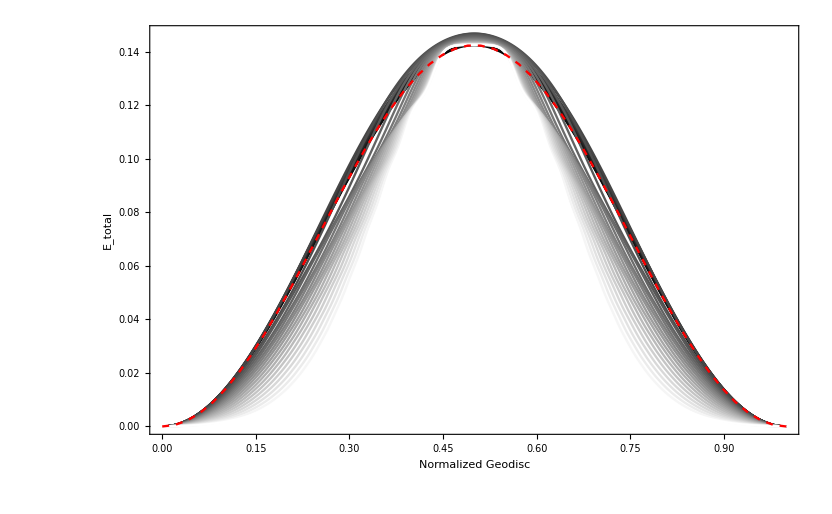

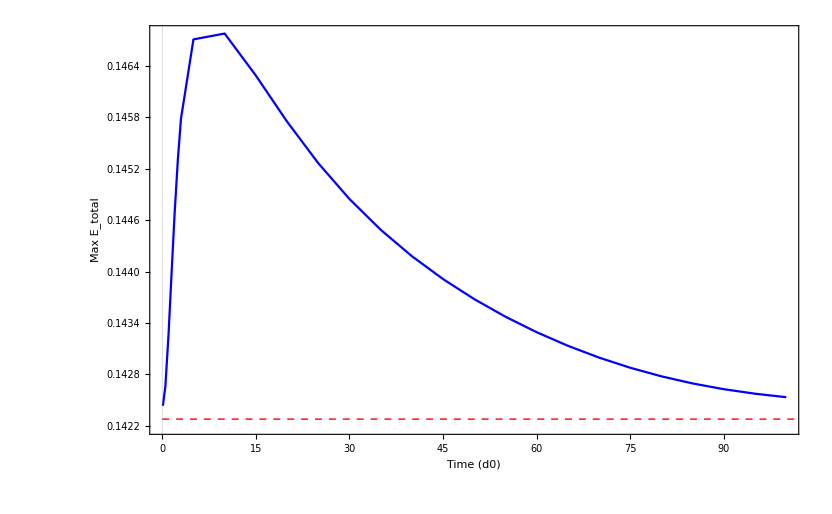

Time | Max E_total
0.1 d0 | 0.142434
0.5 d0 | 0.142659
1. d0 | 0.143253
1.5 d0 | 0.143989
2. d0 | 0.144699
2.5 d0 | 0.145302
3. d0 | 0.14578
5. d0 | 0.146707
10. d0 | 0.146775
15. d0 | 0.146285
20. d0 | 0.145748
25. d0 | 0.145264
30. d0 | 0.144846
35. d0 | 0.144487
40. d0 | 0.144179
45. d0 | 0.143912
50. d0 | 0.143678
55. d0 | 0.143473
60. d0 | 0.143292
65. d0 | 0.143134
70. d0 | 0.142996
75. d0 | 0.142878
80. d0 | 0.142778
85. d0 | 0.142695
90. d0 | 0.142628
95. d0 | 0.142575
100. d0 | 0.142534
MEP | 0.142279

```mathematica
(* ::1::*)(*Define the times:0.1 to 3.0 manually,then 5.0 to 100.0 in steps of 5.0*)timesList={0.1,0.5,1.0,1.5,2.0,2.5,3.0}~Join~Table[5.0 i,{i,1,20}];

(*Helper to format times for file paths,ensuring "1.0" stays "1.0" (not "1.")*)
formatTime[t_?NumericQ]:=Which[FractionalPart[t]==0,ToString[IntegerPart[t]]<>".0",True,ToString[t]];

(*Generate file paths*)
filePaths=Table["C:\\Users\\abhin\\Desktop\\FePt\\I-II\\"<>formatTime[t]<>"d0\\Energy_P.out",{t,timesList}];

(*MEP file*)
mepFile="C:\\Users\\abhin\\Desktop\\FePt\\MEP_I-II\\Energy_G.out";
(*mepFile="C:\\Users\\abhin\\Desktop\\FePt\\I-II\\100.0d0\\Energy_P.out";*)

(* ::2::*)
(*Import,normalize Geodisc,extract E_total,find max E_total*)
parsedData=Table[If[FileExistsQ[filePaths[[i]]],Module[{rawData,data,geodisc,eTotal,minG,maxG},rawData=Import[filePaths[[i]],"Table"];
If[Length[rawData]>=3,data=rawData[[3;;]];
geodisc=data[[All,8]];
eTotal=data[[All,3]];
minG=Min[geodisc];
maxG=Max[geodisc];
normGeodisc=(geodisc-minG)/(maxG-minG);
{timesList[[i]],normGeodisc,eTotal,Max[eTotal]},{timesList[[i]],{},{},"NoData"}]],{timesList[[i]],{},{},"NoData"}],{i,1,Length[filePaths]}];

(*MEP file processing*)
mepData=If[FileExistsQ[mepFile],Module[{rawData,data,geodisc,eTotal,minG,maxG},rawData=Import[mepFile,"Table"];
If[Length[rawData]>=3,data=rawData[[3;;]];
geodisc=data[[All,8]];
eTotal=data[[All,3]];
minG=Min[geodisc];
maxG=Max[geodisc];
normGeodisc=(geodisc-minG)/(maxG-minG);
{"MEP",normGeodisc,eTotal,Max[eTotal]},{"MEP",{},{},"NoData"}]],{"MEP",{},{},"NoData"}];

(*Combine data*)
allData=Join[parsedData,{mepData}];

(* ::3::*)
(*FIRST PLOT:Overlay of normalized Geodisc vs.E_total*)

(*Generate a color gradient from light gray to dark gray*)
colors=Table[GrayLevel[i/(Length[parsedData]-1)],{i,0,Length[parsedData]-1}];

(*Plot the curves*)
overlayPlot=Show[Table[If[allData[[i,2]]==={},Nothing,ListLinePlot[Transpose[{allData[[i,2]],allData[[i,3]]}],PlotStyle->Directive[colors[[i]],Thickness[0.002]]]],{i,1,Length[parsedData]}],(*Add the MEP curve in red,dashed*)ListLinePlot[If[mepData[[2]]==={},Nothing,Transpose[{mepData[[2]],mepData[[3]]}]],PlotStyle->Directive[Red,Dashed,Thickness[0.002]]],PlotRange->All,Frame->True,FrameLabel->{"Normalized Geodisc","E_total"},PlotTheme->"Scientific"];

overlayPlot

(* ::4::*)
(*SECOND PLOT:Time vs.Max E_total,with MEP as a horizontal dashed line*)
timeVsMaxData=Table[{allData[[i,1]],If[allData[[i,4]]==="NoData",Null,allData[[i,4]]]},{i,1,Length[parsedData]}];

(*Extract MEP max value*)
mepMax=If[mepData[[4]]==="NoData",Null,mepData[[4]]];

(*Plot time vs.max E with a dashed horizontal line for MEP*)
maxEPlot=Show[ListPlot[timeVsMaxData,Joined->True,PlotStyle->{Blue,PointSize[0.015]},Frame->True,FrameLabel->{"Time (d0)","Max E_total"},PlotTheme->"Scientific"],Graphics[{Dashed,Red,Line[{{0,mepMax},{105,mepMax}}]}]];

maxEPlot

(* ::5::*)
(*Display table of times (or MEP) and their max E_total*)
resultsTable=Table[{If[NumericQ[allData[[i,1]]],ToString[allData[[i,1]]]<>" d0","MEP"],allData[[i,4]]},{i,1,Length[allData]}];

TableForm[resultsTable,TableHeadings->{None,{"Time","Max E_total"}}]
```